## Resolución del sistema

```mathematica
Clear[alphaMas, alphaMenos, alphaZ, Ω, β]
```

```mathematica
β = 0.075; Ω = 0.4;
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + (I Ω)/2(1 + x[t]^2)== 0 ,y'[t] == I/2(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ (I Ω)/2 == 0, x[-210]==y[-210]==z[-210]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10];
```

```mathematica
alphaMasInterp = Interpolation[Table[{t, alphaMas[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

```mathematica
alphaMenosInterp = Interpolation[Table[{t, alphaMenos[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

```mathematica
alphaZInterp = Interpolation[Table[{t,alphaZ[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

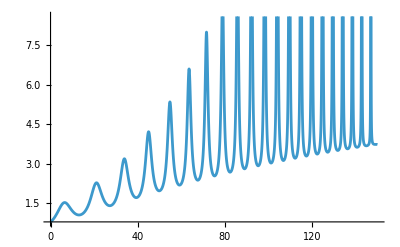

```mathematica
Plot[Re[alphaMasInterp[t]],{t,0,150}]
```

```mathematica
Plot[Re[alphaMas[t]],{t,0,150}]
```

## Espectro EW estado base

PROBABILIDAD TRANSICIÓN

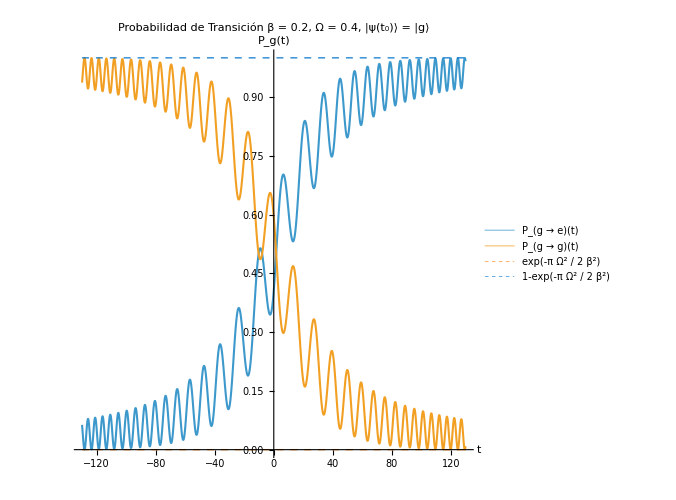

```mathematica
Plot[{(Abs[alphaMasInterp[t]]^2 )Exp[-2Re[alphaZInterp[t]]], Abs[Exp[- alphaZInterp[t]] ]^2,Exp[-π(Ω^2/(2(β^2)))], 1- Exp[-π(Ω^2/(2β^2))]}, {t, -130, 130}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)","exp(-π Ω^2 / 2 β^2)","1-exp(-π Ω^2 / 2 β^2)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,
PlotLabel->Style["Probabilidad de Transición  β = 0.2, Ω = 0.4, |ψ(t_0)⟩ = |g⟩ ", 18, FontFamily->"Times New Roman", Black]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/proba",,"PNG"]
```

```mathematica
P1 = Plot[{(Abs[alphaMasInterp[t]]^2 )Exp[-2Re[alphaZInterp[t]]], 1-Exp[-π(Ω^2/(2(β^2)))]}, {t, -50, 100},PlotRange->{-0.05,1.0}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[RGBColor[0.92,0.5,0.5],Thickness[0.003], Opacity[0.75]], Directive[RGBColor[0.92,0.5,0.5],Thickness[0.002], Dashed]},PlotLegends-> {"Ω=0.1, δ= 0.125"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,
PlotLabel->Style["Probabilidades de Transición  β = 0.2", 18, FontFamily->"Times New Roman", Black]]
```

ENERGY LEVELS

```mathematica
del[T_]:= T β^2;
```

```mathematica
Ω^2/(2 β^2)
```

4.5

```mathematica
Emas[T_, Ω_]:=1/2 Sqrt[Ω^2 +del[T]^2]
```

```mathematica
Plot[{Emas[t, 0.1],Emas[t, 0.2] ,Emas[t, 0.3],1/2 del[t],-1/2 del[t], -Emas[t,0.3],-Emas[t,0.2], -Emas[t,0.1]}, {t, -14, 14}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Directive[Thickness[0.004], RGBColor[0.24,0.5,0.74]],Directive[Thickness[0.004], RGBColor[0.81,0.27,0.18]],Directive[Thickness[0.004], RGBColor[0.63,0.5,0.16]],Directive[Thickness[0.003], Dashed, RGBColor[0.01,0.42,0.14]],Directive[Thickness[0.003], Dashed, RGBColor[0.4,0.18,0.05]],Directive[Thickness[0.004], RGBColor[0.63,0.5,0.16]] ,
Directive[Thickness[0.004], RGBColor[0.81,0.27,0.18]],Directive[Thickness[0.004], RGBColor[0.24,0.5,0.74]]},
PlotLegends->{Style["Ω=0.1, δ= 0.125"], Style["Ω=0.2, δ= 0.5"], Style["Ω=0.3, δ= 1.125"] , Style["E_↓",RGBColor[0.01,0.42,0.14] ],Style["E_↑",RGBColor[0.4,0.18,0.05] ] },AxesOrigin->{-14,-0.318},
AxesLabel-> {Style["Time",16,GrayLevel[0.26]] , Style["Energy",16, GrayLevel[0.26]]}, AspectRatio->1, ImageSize->500]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/niveles",,"PNG"]
```

INTEGRALES

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZInterp[t]]alphaMenosInterp[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZInterp[t]]alphaMenosInterp[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

ESPECTRO

```mathematica
Γ = 0.1;T = -200;T0=-220;Ωr = Sqrt[(T*β^2)^2 + Ω^2 ];ν=1.4;
```

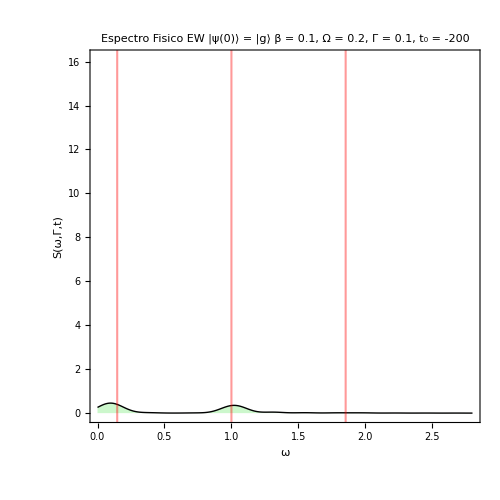

```mathematica
ListLinePlot[ParallelTable[{ω,S[Γ,ω*ν-ν,T,T0]},{ω,0,2*ν,(2*ν)/400}],PlotRange->{-0.1,16.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->{{14,2},{14,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω",16,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",16,FontFamily->"Times New Roman",Gray]},
 ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
GridLines->{{{1,Directive[Thickness[0.003],Red]},{(ν-Ωr)/ν,Directive[Thickness[0.003],Red]},{ (ν+Ωr)/ν,Directive[Thickness[0.003],Red]}},None}, PlotLabel->Style["Espectro Fisico EW   |ψ(0)⟩ = |g⟩ \n β = 0.1, Ω = 0.2, Γ = 0.1, t_0 = -200", 16, FontFamily->"Times New Roman", Black]]
```

```mathematica
P1 = ListLinePlot[ParallelTable[{ω,S[Γ,ω*ν-ν,T,T0]},{ω,0,2*ν,(2*ν)/400}],PlotRange->{-0.1,16.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->{{14,2},{14,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω",16,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",16,FontFamily->"Times New Roman",Gray]},
 ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
GridLines->{{{1,Directive[Thickness[0.003],Red]},{(ν-Ωr)/ν,Directive[Thickness[0.003],Red]},{ (ν+Ωr)/ν,Directive[Thickness[0.003],Red]}},None}, PlotLabel->Style["Espectro Fisico EW   |ψ(0)⟩ = |g⟩ \n β = 0.1, Ω = 0.2, Γ = 0.1, t_0 = -200", 16, FontFamily->"Times New Roman", Black]];

P2 = Plot[{(Abs[alphaMasInterp[t]]^2 )Exp[-2Re[alphaZInterp[t]]], Abs[Exp[- alphaZInterp[t]] ]^2}, {t, -150, 180}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->360,
GridLines->{{{T,Directive[Thickness[0.003],Darker[Red]]}},None},AxesOrigin->{-150,0},
PlotLabel->Style["Probabilidad de Transición, t = 16", 16, FontFamily->"Times New Roman", Black]];
```

```mathematica
GraphicsRow[{P1,P2}, AspectRatio->Full,  ImageSize->1000, Alignment->Top]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/dicu/lineal/espectroLZ_beta01_omega04/t=-140",,"PNG"]
```

ESPECTRO

```mathematica
ωMin=-2.2;ωMax=2.2;ωSteps=100;
tMin=-40;tMax=40;tSteps=100;

(*Generate grid of values using ParallelTable*)
data=ParallelTable[{t,ω,S[Γ,ω,t,T0]},{ω,ωMin,ωMax,0.025},{t,tMin,tMax,0.5}];

(*Flatten the data for ListDensityPlot*)
flatData=Flatten[data,1];

(*Create the density plot*)
ListDensityPlot[flatData,InterpolationOrder->1,ColorFunction->"RedBlueTones",FrameLabel->{"ω","t"},PlotLegends->Automatic]
```

## Espectro EW estado excitado

TRANSICIÓN DEL ESTADO EXCITADO

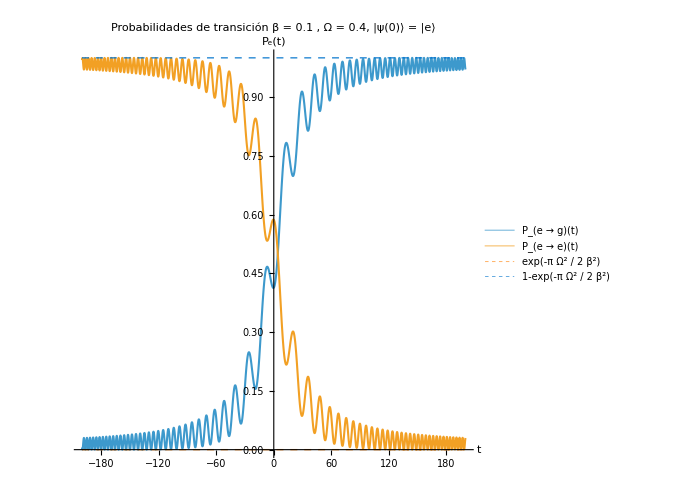

```mathematica
Plot[{(Abs[alphaMenosInterp[t]]^2) Exp[-2Re[alphaZInterp[t]]], Abs[Exp[alphaZInterp[t]] + Exp[-alphaZInterp[t]] alphaMasInterp[t] alphaMenosInterp[t]]^2, Exp[-π(Ω^2/(2(β^2)))], 1- Exp[-π(Ω^2/(2β^2))]}, {t, -200, 200},
PlotLabel->Style["Probabilidades de transición  β = 0.1 , Ω = 0.4, |ψ(0)⟩ = |e⟩ ", 18, FontFamily->"Times New Roman", Black],PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},
PlotLegends-> {"P_(e  → g)(t)", "P_(e → e)(t)", "exp(-π Ω^2 / 2 β^2)","1-exp(-π Ω^2 / 2 β^2)"},FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1,ImageSize->500,AxesLabel-> {Style["t",14,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_e(t)",13,FontFamily->"Times New Roman",GrayLevel[0.26]]}]
```

Integrales

```mathematica
L1[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZInterp[t]]alphaMenosInterp[t], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
L2[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZInterp[t]], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S2[Γ_,ω_,T_,T0_]:=2Γ Exp[-2Γ T](L1[Γ,ω,T,T0]+L2[Γ,ω,T,T0])
```

## Comparacion Mollow

```mathematica
SBas[ω_] := ((Ω/Ωr)^2)((Γ (1-Δ/Ωr))/(4 (Γ^2 +(ω-ν-Ωr)^2))+(1/2 Γ)/(Γ^2 + (ω-ν)^2)+(Γ (1+Δ/Ωr))/(4 (Γ^2+(ω-ν+Ωr)^2))) ;
```

```mathematica
SExc[ω_] := (Γ/8((1+(Δ/Ωr)^2-2(Δ/Ωr))(Ω/Ωr)^2 +(1-Δ/Ωr)^4))/(Γ^2 +(ω-ν-Ωr)^2)+(Γ/2(((Δ/Ωr)^2)((Ω/Ωr)^2) +(1-Δ^2/Ωr^2)^2))/(Γ^2 + (ω-ν)^2)+(Γ/8((1+(Δ/Ωr)^2+2(Δ/Ωr))(Ω/Ωr)^2 +(1+Δ/Ωr)^4))/(Γ^2+(ω-ν+Ωr)^2);
```

```mathematica
T0=-200;T =24;Γ = 0.1;ν=1.2; Ωr = Sqrt[ (T*β^2)^2+ Ω^2];Δ=-T*β^2;
```

```mathematica
ωmin = (ν-1.2)/ν;ωmax = (ν+1.2)/ν;
```

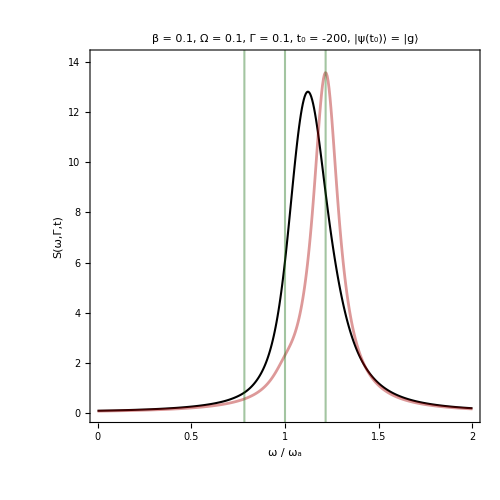

```mathematica
P1 = Show[{ListLinePlot[ParallelTable[{ω,S[Γ,ω*ν -ν,T,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/400}],PlotRange->{-0.1,14.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->{{14,2},{14,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω / ω_a",16,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",16,FontFamily->"Times New Roman",Gray]},
 ImageSize->500,GridLines->{{{1,Directive[Thickness[0.003],RGBColor[0.1,0.43,0.08]]},{(ν-Ωr)/ν,Directive[Thickness[0.003],RGBColor[0.1,0.43,0.08]]},{ (ν+Ωr)/ν,Directive[Thickness[0.003],RGBColor[0.1,0.43,0.08]]}},None},PlotLabel->Style["β = 0.1, Ω = 0.1, Γ = 0.1, t_0 = -200, |ψ(t_0)⟩ = |g⟩", 16, FontFamily->"Times New Roman", Black]],ListLinePlot[ParallelTable[{ω,SExc[ω*ν]*0.76},{ω,ωmin,ωmax,(ωmax-ωmin)/400}],Joined->True,AxesOrigin->None,PlotRange->{-0.1,14.2},
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.004], Opacity[0.4]],FrameTicksStyle->{{14,2},{14,20}},PlotRangePadding->0,AspectRatio->1,ImageSize->500]},FrameTicks->{{{0,2,4,6,8,10,12,14,16},None},{{0,0.5,1,1.5,2},None}},PlotRange->{-0.1,14.2}];

P3 = Plot[{(Abs[alphaMasInterp[t]]^2 )Exp[-2Re[alphaZInterp[t]]], Abs[Exp[- alphaZInterp[t]] ]^2}, {t, -80, 80}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->360,
GridLines->{{{T,Directive[Thickness[0.003],Darker[Red]]}},None},AxesOrigin->{-80,0},
PlotLabel->Style["Probabilidad de Transición, t = 24", 16, FontFamily->"Times New Roman", Black]];

GraphicsRow[{P1,P3}, AspectRatio->Full,  ImageSize->1000, Alignment->Top]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/Dicu/lineal/beta01_omega01_initial_ground/t=24",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/Dicu/lineal/beta01_omega01_initial_ground/t=24

## Comparacion Lineal Limite

```mathematica
EWLinear[Γ_,β_,ω_,T_]:=(π Γ)/(2 β^2)Exp[-2 Γ (T-ω /(2β^2))]Abs[Erfc[(I^(1/2))(Γ-I (ω-2T β^2))/(2β)]]^2
```

```mathematica
T0=-220;T = 30;Γ = 0.1;ν=4.4; Ωr = Sqrt[ (T*β^2)^2+ Ω^2];Δ=-T*β^2;
```

```mathematica
ωmin = (ν-1.4)/ν;ωmax = (ν+4.4)/ν;
```

```mathematica
G1 =Show[{ListLinePlot[ParallelTable[{ω,0+S[Γ,ω*ν -ν,0,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,60.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=0",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,0+EWLinear[Γ,β/Sqrt[2],ω*ν-ν,0]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,60.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

```mathematica
G2 =Show[ListLinePlot[ParallelTable[{ω,15+S[Γ,ω*ν -ν,30,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,60.2},Filling->15,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=30",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,15+EWLinear[Γ,β/Sqrt[2],ω*ν-ν,30]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,60.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]]
```

```mathematica
G3 =Show[ListLinePlot[ParallelTable[{ω,30+S[Γ,ω*ν -ν,60,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,60.2},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=60",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,30+EWLinear[Γ,β/Sqrt[2],ω*ν-ν,60]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,60.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]]
```

```mathematica
G4 =Show[ListLinePlot[ParallelTable[{ω,45+S[Γ,ω*ν -ν,90,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,60.2},Filling->45,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=90",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,45+EWLinear[Γ,β/Sqrt[2],ω*ν-ν,90]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,60.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]]
```

```mathematica
G5 =Show[ListLinePlot[ParallelTable[{ω,67+S[Γ,ω*ν -ν,120,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,86.5},Filling->67,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=120",
FrameLabel->{Style["ω / ω_a",18,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",18,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],
ListLinePlot[ParallelTable[{ω,67+EWLinear[Γ,β/Sqrt[2],ω*ν-ν,120]},{ω,ωmin,ωmax,(ωmax-ωmin)/500}],PlotRange->{-0.5,86.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]]
```

```mathematica
Show[{G4,G3,G2,G1}, PlotLabel-> Style["β = 0.2, Ω = 0.2, Γ = 0.1, t_0 = -220", 18, FontFamily->"Times New Roman", Black]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/limite_lineal2",,"PNG"]
```

## Solución hiperbolica

## Solución Periodica